2.2×10^-6

299792458

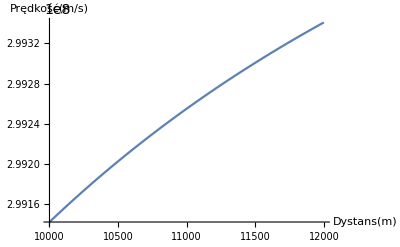

```mathematica
ClearAll["global`*"]
t = 2.2*10^(-6) (*s*)
c = 299792458 (*m/s*)
(*v = 1/Sqrt[(t^2/S^2)+1/c^2]*)

Show[Plot[1/Sqrt[(t^2/S^2)+1/c^2],{S, 10000, 12000}],AxesLabel->{HoldForm[Dystans[m]],HoldForm[Prędkość[m/s]]},PlotLabel->None,LabelStyle->{FontFamily->"FreeSans",GrayLevel[0]}]
```

Zadanie 6, grupa C
Zadanie rozwiązywane w większości na papierze, Solve[] nie dał rady. Wychodził błąd przekroczenia limitu rekurencji.
Wyprowadzone za pomocą wzoru na dylatacje czasu, doprowadzone do formy
v = 1/Sqrt[(t^2/S^2)+1/c^2]
Grzegorz Koperwas, grupa C2